# Auxiliary Functions

This section defines some auxiliary functions used to read LATEX input into Mathematica

```mathematica
Quiet@Remove["Global`*"]
FormattingStrings[string_]:=Block[{},
auxiliarystring=StringReplace[string,"+ "->"+"];
auxiliarystring=StringReplace[auxiliarystring," +"->"+"];
auxiliarystring=StringReplace[auxiliarystring,"- "->"-"];
auxiliarystring=StringReplace[auxiliarystring," -"->"-"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot "->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\cdot"->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," "->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot"->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\times"->" \\times "];
auxiliarystring=StringReplace[auxiliarystring,"\\mu_{NF}"->"{muNF}"];
auxiliarystring=ToExpression[auxiliarystring,TeXForm];
Return[auxiliarystring]
]
FormattingStringsCommaSplit[string_]:=Block[{},
auxiliarystring=StringReplace[string,"+ "->"+"];
auxiliarystring=StringReplace[auxiliarystring," +"->"+"];
auxiliarystring=StringReplace[auxiliarystring,"- "->"-"];
auxiliarystring=StringReplace[auxiliarystring," -"->"-"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot "->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\cdot"->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," "->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot"->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\times"->" \\times "];
auxiliarystring=StringReplace[auxiliarystring,"\\mu_{NF}"->"{muNF}"];
auxiliarystring=StringSplit[auxiliarystring,","];
Return[auxiliarystring]
]
```

# Vector field

This section loads the List of Kinetics and variables and finds the equilibria of the system if eqbool=1. Otherwise, it only loads Kinetics. This cell requires some input only if Mathematica finds more than one homogeneous steady-state

```mathematica
SetDirectory[NotebookDirectory[]];
null[_String]:=Null;
eqbool=1;
If[FileExistsQ["Kinetics.txt"],
nvar=Length@ReadList["Kinetics.txt",null@String,NullRecords->True];
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'Kinetics.txt' was not found. Run the Python script first."}],"Output"]];
Quit[];
]
kinetics=Range[nvar];
var=Range[nvar];
For[varnum=1,varnum<=nvar,varnum++,
kinetics[[varnum]]=ReadLine["Kinetics.txt"];
kinetics[[varnum]]=FormattingStrings[kinetics[[varnum]]];
If[FileExistsQ["List of variables.txt"],
var[[varnum]]=ReadLine["List of variables.txt"];
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'List of variables.txt' was not be found. Run the Python script first."}],"Output"]];
Quit[]
];
var[[varnum]]=ToExpression[var[[varnum]],TeXForm];
];
Close["Kinetics.txt"];
Close["List of variables.txt"];
If[eqbool==1,
eqs=Solve[kinetics==0,var];
If[Length[eqs]>1,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"Your system has " <> ToString[Length[eqs]] <> " equilibria"}],"Output"]];
For[eqnum=1,eqnum<=Length[eqs],eqnum++,
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"Equilibrium number " <> ToString[eqnum] <> " is equal to ",ToString[eqs[[eqnum]],FormatType->StandardForm]}],"Output"]];];
eqnumber=Input["Enter the number of the equilibrium point you would like to consider. Enter 0 if the software did not find your desired homogeneous steady-state or you want to consider them all"];
NotebookClose[aux];
If[eqnumber==0,
eq={0};
,
eq=eqs[[eqnumber]]//Simplify;]
,
Print["Mathematica found only one homogeneous steady-state in your system. It will proceed with that one."];
eq=eqs[[1]]//Simplify;
]
,
eq={0};
]
(*First equilibrium*)
```

# Turing bifurcation variables and Fixed parameters

This section loads the functions required to find and continue Turing bifurcations, and evaluates the parameters that remain fixed throughout the computation

```mathematica
If[FileExistsQ["Third-order coefficient.txt"],
C3=Import["Third-order coefficient.txt"];
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'Third-order coefficient.txt' was not found. Run the Python script first."}],"Output"]];
Quit[];
]
C3=FormattingStrings[C3];
If[FileExistsQ["Determinant of the Jacobian matrix.txt"],
zerodet=Import["Determinant of the Jacobian matrix.txt"];
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'Determinant of the Jacobian matrix.txt' was not found. Run the Python script first."}],"Output"]];
Quit[];
]
zerodet=FormattingStrings[zerodet];
If[FileExistsQ["Derivative of the Determinant.txt"],
zeroder=Import["Derivative of the Determinant.txt"];
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'Derivative of the Determinant.txt' was not found. Run the Python script first."}],"Output"]];
Quit[];
]
zeroder=FormattingStrings[zeroder];
If[FileExistsQ["Fixed parameter values.txt"],
Nparametereval=Length@ReadList["Fixed parameter values.txt",null@String,NullRecords->True];
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'Fixed parameter values.txt' was not found. Run the Python script first."}],"Output"]];
Quit[];
]
If[Nparametereval>0,
For[parnum=1,parnum<=Nparametereval,parnum++,
aux=ReadLine["Fixed parameter values.txt"];
aux=FormattingStringsCommaSplit[aux];
parname=ToExpression[aux[[1]],TeXForm];
parval=ToExpression[aux[[2]],TeXForm];
parname//Evaluate=parval;
];
Close["Fixed parameter values.txt"];
]
```

# Parameters on the axes of the bifurcation diagram

In this section, Mathematica loads the file with the parameters on the axes of the bifurcation diagram and the intervals over which they change

```mathematica
npar=2;
par=Range[npar];
lowerbound=Range[npar];
upperbound=Range[npar];
For[parnum=1,parnum<=npar,parnum++,
If[FileExistsQ["Parameters on axes.txt"],
aux=ReadLine["Parameters on axes.txt"];
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"The file 'Parameters on axes.txt' was not found. Run the Python script first."}],"Output"]];
Quit[]
];
aux=FormattingStringsCommaSplit[aux];
par[[parnum]]=ToExpression[aux[[1]],TeXForm];
lowerbound[[parnum]]=ToExpression[aux[[2]],TeXForm];
upperbound[[parnum]]=ToExpression[aux[[3]],TeXForm];
]
Close["Parameters on axes.txt"];
If[FileExistsQ["Actual names of parameters.txt"],
aux=ReadLine["Actual names of parameters.txt"];
aux=FormattingStringsCommaSplit[aux];
newparam1=ToExpression[aux[[1]],TeXForm];
newparam2=ToExpression[aux[[2]],TeXForm];
Close["Actual names of parameters.txt"];
,
newparam1=par[[1]];
newparam2=par[[2]];
];
```

# Bifurcation curves

In this section, this script reads the file “Initial conditions for Turing bifurcation curves” and goes fixing one parameter leaving the other parameter and μ free to solve the two equations that determine a Turing bifurcation curve. Then, the script poses an ordinary differential equation to use the method of pseudo-arclength continuation to continue the bifurcation curves as the parameters change. NOTE: Here, the variable “time” is just an auxiliary variable that can be understood as the arclength of the bifurcation curve but it has nothing to do with the actual time in the reaction-diffusion equation

```mathematica
initialt=-1000;
finalt=1000;
curvespeed=1;
tol=10^-9;
Choptol=10^-9;
simpleeq=1;
smalldifferential=0.001;
variabledependence=Table[var[[varnum]]->var[[varnum]][time],{varnum,nvar}];
kineticsaux=kinetics/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.variabledependence;
zerodetaux=zerodet/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.variabledependence;
zeroderaux=zeroder/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.variabledependence;
equations=Append[kineticsaux,zerodetaux];
AppendTo[equations,zeroderaux];
equations=D[equations,time];
AppendTo[equations,(par[[1]]'[time])^2+(par[[2]]'[time])^2+muNF'[time]^2+∑_(varnum=1)^nvar (var[[varnum]]'[time])^2-curvespeed^2];
equations=Table[equations[[equationnumber]]==0,{equationnumber,Length[equations]}];
equationsGlobalLP=Append[kineticsaux,zerodetaux/.muNF[time]->0];
equationsGlobalLP=D[equationsGlobalLP,time];
AppendTo[equationsGlobalLP,(par[[1]]'[time])^2+(par[[2]]'[time])^2+∑_(varnum=1)^nvar (var[[varnum]]'[time])^2-curvespeed^2];
equationsGlobalLP=Table[equationsGlobalLP[[equationnumber]]==0,{equationnumber,Length[equationsGlobalLP]}];
allvar=Table[var[[varnum]],{varnum,nvar}];
AppendTo[allvar,par[[1]]];
AppendTo[allvar,par[[2]]];
AppendTo[allvar,muNF];
allvartimedependent=Table[allvar[[nvar]][time],{nvar,Length[allvar]}];
allvarGlobalLP=Table[var[[varnum]],{varnum,nvar}];
AppendTo[allvarGlobalLP,par[[1]]];
AppendTo[allvarGlobalLP,par[[2]]];
allvarGlobalLPtimedependent=Table[allvarGlobalLP[[nvar]][time],{nvar,Length[allvarGlobalLP]}];
If[FileExistsQ["Initial conditions for Turing bifurcation curves.txt"],
numberofbifurcationcurves=Length@ReadList["Initial conditions for Turing bifurcation curves.txt",null@String,NullRecords->True];
,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"Initial conditions for Turing bifurcation curves.txt' was not found. Run the Python script first."}],"Output"]];
Quit[];
]
initialvalueTuring={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
aux=ReadLine["Initial conditions for Turing bifurcation curves.txt"];
aux=FormattingStringsCommaSplit[aux];
AppendTo[initialvalueTuring,{ToExpression[aux[[1]],TeXForm],ToExpression[aux[[2]],TeXForm]}];
]
Close["Initial conditions for Turing bifurcation curves.txt"];
solutioncurves={};
solutioncurvesGlobalLP={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
fixedparameter=Position[par,initialvalueTuring[[bifnum]][[1]]][[1]][[1]];
If[fixedparameter==1,
anotherparameter=2;
,
anotherparameter=1;
];
If[Length[eq]==1 || simpleeq==0,
initialvalues=Quiet@NSolve[Join[{zerodet,zeroder},kinetics]==0/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],Join[{par[[anotherparameter]],muNF},var]//Evaluate];
initialvaluesGlobalLP=Quiet@NSolve[Join[{zerodet},kinetics]==0/.muNF->0/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],Join[{par[[anotherparameter]]},var]//Evaluate];
,
initialvalues=Quiet@NSolve[{zerodet,zeroder}==0/.eq/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],{par[[anotherparameter]],muNF}//Evaluate];
initialvaluesGlobalLP=Quiet@NSolve[zerodet==0/.muNF->0/.eq/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],par[[anotherparameter]]//Evaluate];
];
initialvalues=Table[Table[initialvalues[[initialsolnum]][[varnum]][[1]]->Re[initialvalues[[initialsolnum]][[varnum]][[2]]],{varnum,Length[initialvalues[[initialsolnum]]]}],{initialsolnum,Length[initialvalues]}];
initialvalues=DeleteDuplicates[initialvalues];
For[initialsolnum=1,initialsolnum<=Length[initialvalues],initialsolnum++,
AppendTo[initialvalues[[initialsolnum]],par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]];
If[simpleeq==1 && Length[eq]>1,
Quiet @ If[¬(var∈Reals)/.eq/.initialvalues[[initialsolnum]],Continue[]];
initialvalues[[initialsolnum]]=Join[initialvalues[[initialsolnum]],Table[var[[varnum]]->(var[[varnum]]/.eq/.initialvalues[[initialsolnum]]),{varnum,nvar}]]
];
If[If[Length[eq]==1,
Activate[Inactivate[Chop[muNF,Choptol]!=0 &&
Max[Abs[Join[{zerodet,zeroder},kinetics]]]<tol && lowerbound[[anotherparameter]]<=par[[anotherparameter]]<=upperbound[[anotherparameter]]]/.initialvalues[[initialsolnum]]],
Activate[Inactivate[Chop[muNF,Choptol]!=0 &&
Max[Abs[{zerodet,zeroder}]]<tol && Norm[(var/.eq)-var]<tol && lowerbound[[anotherparameter]]<=par[[anotherparameter]]<=upperbound[[anotherparameter]]]/.initialvalues[[initialsolnum]]]],
dereval=Table[initialvalues[[initialsolnum]][[varnum]][[1]][0]->initialvalues[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvalues[[initialsolnum]]]}];
initialderivatives=Quiet@Solve[equations/.time->0/.dereval,D[allvartimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Join[equations,Table[initialvalues[[initialsolnum]][[varnum]][[1]][0]==initialvalues[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvalues[[initialsolnum]]]}]];
equationsaux=Join[equationsaux,Table[initialderivatives[[dernumber]][[varnum]][[1]]==initialderivatives[[dernumber]][[varnum]][[2]],{varnum,Length[initialderivatives[[dernumber]]]}]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==lowerbound[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==upperbound[[1]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==lowerbound[[2]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==upperbound[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
sol=Quiet@NDSolve[equationsaux,allvar,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
tempplot=Quiet@ParametricPlot[{If[(muNF[time]/.sol)∈Reals,{par[[1]][time],par[[2]][time]}/. sol]},{time,sol[[1]][[1]][[2]]["Domain"][[1]][[1]],sol[[1]][[1]][[2]]["Domain"][[1]][[2]]},AspectRatio->1,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}];
If[Length[Cases[Normal@tempplot,Line[x_]:>x,Infinity]]>0,
AppendTo[solutioncurves,sol];
]
]
]
];
initialvaluesGlobalLP=Table[Table[initialvaluesGlobalLP[[initialsolnum]][[varnum]][[1]]->Re[initialvaluesGlobalLP[[initialsolnum]][[varnum]][[2]]],{varnum,Length[initialvaluesGlobalLP[[initialsolnum]]]}],{initialsolnum,Length[initialvaluesGlobalLP]}];
initialvaluesGlobalLP=DeleteDuplicates[initialvaluesGlobalLP];
For[initialsolnum=1,initialsolnum<=Length[initialvaluesGlobalLP],initialsolnum++,
AppendTo[initialvaluesGlobalLP[[initialsolnum]],par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]];
If[simpleeq==1 && Length[eq]>1,
Quiet@If[¬(var∈Reals)/.eq/.initialvaluesGlobalLP[[initialsolnum]],Continue[]];
initialvaluesGlobalLP[[initialsolnum]]=Join[initialvaluesGlobalLP[[initialsolnum]],Table[var[[varnum]]->(var[[varnum]]/.eq/.initialvaluesGlobalLP[[initialsolnum]]),{varnum,nvar}]]
];
If[If[Length[eq]==1,Activate[Inactivate[Max[Abs[Append[kinetics,zerodet/.muNF->0]]]<tol && lowerbound[[anotherparameter]]<=par[[anotherparameter]]<=upperbound[[anotherparameter]]]/.initialvaluesGlobalLP[[initialsolnum]]],Activate[Inactivate[Abs[zerodet/.muNF->0]<tol && Norm[(var/.eq)-var]<tol && lowerbound[[anotherparameter]]<=par[[anotherparameter]]<=upperbound[[anotherparameter]]]/.initialvaluesGlobalLP[[initialsolnum]]]],
dereval=Table[initialvaluesGlobalLP[[initialsolnum]][[varnum]][[1]][0]->initialvaluesGlobalLP[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvaluesGlobalLP[[initialsolnum]]]}];
initialderivatives=Quiet@Solve[equationsGlobalLP/.time->0/.dereval,D[allvarGlobalLPtimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Join[equationsGlobalLP,Table[initialvaluesGlobalLP[[initialsolnum]][[varnum]][[1]][0]==initialvaluesGlobalLP[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvaluesGlobalLP[[initialsolnum]]]}]];
equationsaux=Join[equationsaux,Table[initialderivatives[[dernumber]][[varnum]][[1]]==initialderivatives[[dernumber]][[varnum]][[2]],{varnum,Length[initialderivatives[[dernumber]]]}]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==lowerbound[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==upperbound[[1]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==lowerbound[[2]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==upperbound[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
sol=Quiet@NDSolve[equationsaux,allvar,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
tempplot=Quiet@ParametricPlot[{par[[1]][time],par[[2]][time]}/. sol,{time,sol[[1]][[1]][[2]]["Domain"][[1]][[1]],sol[[1]][[1]][[2]]["Domain"][[1]][[2]]},AspectRatio->1,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}];
If[Length[Cases[Normal@tempplot,Line[x_]:>x,Infinity]]>0,
AppendTo[solutioncurvesGlobalLP,sol];
]
]
]
]
]
If[Length[solutioncurves]==0 && Length[solutioncurvesGlobalLP]==0,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"This script could not find a Turing bifurcation curve or a BD-line for your desired parameters. Try changing tolerances or lines to search."}],"Output"]]]
```

# Finding codimension-two bifurcation points and computing fifth-order coefficient

In this section, the script finds zeroes of the third-order coefficient along Turing bifurcation curves. To do that, it firsts evaluates the C_3 at different points of the bifurcation curves looking for changes of sign. In particular, if the product of C_3 at two different consecutive points is negative, then one of those points si saved to be used as an initial condition to find the actual root of C_3.

```mathematica
Catch[If[Length[solutioncurves]==0 && Length[solutioncurvesGlobalLP]==0,
Throw["This script could not find a bifurcation curve for this system"];
,
timedifference=1;
disttol=10^-6;
tol=10^-6;
criticalitybool=Import["Find codimension-two bifurcation points.txt"];
If[ToString[criticalitybool]=="y",
If[FileExistsQ["Fifth-order coefficient.txt"],
nC5Bool=Length@ReadList["Fifth-order coefficient.txt",null@String,NullRecords->True];
];
If[ValueQ[nC5Bool] && nC5Bool>0,
C5=Import["Fifth-order coefficient.txt"];
C5=FormattingStrings[C5];
fifthcoeff={};
];
initialconditionsforcriticalitychanges={};
For[outersolnum=1,outersolnum<=Length[solutioncurves],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves[[outersolnum]]],innersolnum++,
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C3/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
allvals=Table[{time,auxC3[time]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]],timedifference}];
vals={};
For[valnum=1,valnum<=Length[allvals]-1,valnum++,
If[allvals[[valnum]][[2]]*allvals[[valnum+1]][[2]]<0 && allvals[[valnum]][[1]]>solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],
AppendTo[vals,allvals[[valnum]][[1]]]
]
];
For[tnum=1,tnum<=Length[vals],tnum++,
initialvalueoft=vals[[tnum]];
critchangetemp=time/.Quiet@FindRoot[auxC3[time],{time,initialvalueoft}];
If[solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]]<=critchangetemp<=solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]] && Abs[auxC3[time]/.time->critchangetemp]<tol && (muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp)>0,
auxiliaryarray=Join[{par[[1]]->(par[[1]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),par[[2]]->(par[[2]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),muNF->(muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]])},Table[var[[varnum]]->(var[[varnum]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),{varnum,nvar}]]/.time->critchangetemp;
AppendTo[initialconditionsforcriticalitychanges,auxiliaryarray];
If[nC5Bool>0,
AppendTo[fifthcoeff,{{par[[1]][time],par[[2]][time]}/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp,{C5/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp}}];
Break[]
]
]
]
]
];
If[Length[initialconditionsforcriticalitychanges]>0,
initialconditionsforcriticalitychanges=Join[{par[[1]],par[[2]],muNF},var]/.initialconditionsforcriticalitychanges;
initialconditionsforcriticalitychanges=DeleteDuplicates[initialconditionsforcriticalitychanges,EuclideanDistance[##]<disttol&];
critchange=Table[{par[[1]]->initialconditionsforcriticalitychanges[[critnum]][[1]],par[[2]]->initialconditionsforcriticalitychanges[[critnum]][[2]]},{critnum,Length[initialconditionsforcriticalitychanges]}];
initialconditionsforcriticalitychanges=Table[Join[{par[[1]]->initialconditionsforcriticalitychanges[[critnum]][[1]],par[[2]]->initialconditionsforcriticalitychanges[[critnum]][[2]],muNF->initialconditionsforcriticalitychanges[[critnum]][[3]]},Table[var[[varnum]]->initialconditionsforcriticalitychanges[[critnum]][[3+varnum]],{varnum,nvar}]],{critnum,Length[initialconditionsforcriticalitychanges]}];
If[ValueQ[fifthcoeff],
auxarr={};
For[critnum=1,critnum<=Length[critchange],critnum++,
getout=0;
For[fifthnum=1,fifthnum<=Length[fifthcoeff],fifthnum++,
If[getout==0 && fifthcoeff[[fifthnum]][[1]]=={par[[1]],par[[2]]}/.critchange[[critnum]],
AppendTo[auxarr,fifthcoeff[[fifthnum]]];
getout=1;
]
]
];
fifthcoeff=auxarr;
];
If[Length[critchange]>0,Export["Initial conditions for Codimension-two bifurcation curves.mx",initialconditionsforcriticalitychanges]];
If[ValueQ[fifthcoeff] && Length[fifthcoeff]>0,Export["Fifth-order coefficient at codimension-two bifurcation points.txt",fifthcoeff];
,
If[ValueQ[critchange] && Length[critchange]>0,Export["Codimension-two bifurcation points.txt",critchange]];
]
]
]
]
]
```

# Bifurcation diagram plotting

This section plots each of the parametric bifurcation curves found colored according to the sign of μ and C_3. In particular, if μ>0 and C_3>0 (respectively, C_3<0), then the curve will be coloured Blue (respectively, red). On the othe hand, if μ<0, then the curve will be green dotted. Besides, if μ=0, then the curve will be plotted Gray. Also, if the codimension-two bifurcation points were found in the previous step, they will be plotted in the graph

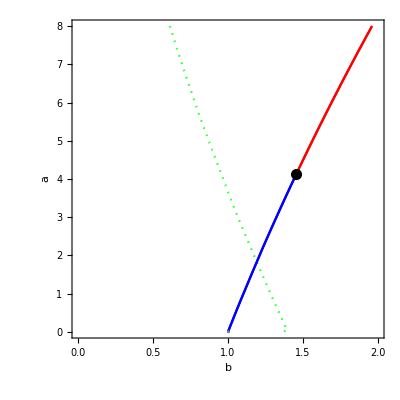

```mathematica
Catch[If[Length[solutioncurves]==0 && Length[solutioncurvesGlobalLP]==0,
Throw["This script could not find a bifurcation curve for this system"];
,
If[ValueQ[critchange] && Length[critchange]>=1,
critpoints=Table[Graphics[{PointSize[0.02],Point[{par[[1]],par[[2]]}/.critchange[[critnum]]]}],{critnum,Length[critchange]}];
];
bifcurveplot={};
GlobalLPplot={};
For[outersolnum=1,outersolnum<=Length[solutioncurves],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves[[outersolnum]]],innersolnum++,
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C3/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
tempplot=Quiet@ParametricPlot[{If[muNF[time]∈Reals && muNF[time]>0 && auxC3[time]∈Reals && auxC3[time]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[muNF[time]∈Reals && muNF[time]>0 && auxC3[time]∈Reals && auxC3[time]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[muNF[time]∈Reals && muNF[time]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],
If[muNF[time]==0/.solutioncurves[[outersolnum]][[innersolnum]] ,{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Red,Blue,{Green,Dotted},Gray},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}];
AppendTo[bifcurveplot,tempplot];
]
];
For[outersolnum=1,outersolnum<=Length[solutioncurvesGlobalLP],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurvesGlobalLP[[outersolnum]]],innersolnum++,
tempplot=Quiet@ParametricPlot[{par[[1]][time],par[[2]][time]}/. solutioncurvesGlobalLP[[outersolnum]][[innersolnum]],{time,solutioncurvesGlobalLP[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurvesGlobalLP[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Gray},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}];
AppendTo[GlobalLPplot,tempplot];
]
];
bifcurveplot=Join[bifcurveplot,GlobalLPplot];
CreateDocument[Dynamic[plot2],WindowSize->{500,500}];
If[ValueQ[critpoints],
plot2=Show[bifcurveplot,critpoints,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1] 
,
plot2=Show[bifcurveplot,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]
]
]
]
```

# Parameters on the axes of the 3D bifurcation diagram

This section loads the extra parameter that will be on the codimension-two plotter

```mathematica
checker=1;
If[!FileExistsQ["Codimension-two parameters on axes.txt"] || !ValueQ[critchange] || Length[critchange]==0 ||!FileExistsQ["Initial conditions for Codimension-two bifurcation curves.mx"],
checker=0;
]
If[checker==1,
npar=3;
auxpar=par;
par=Range[npar];
lowerbound=Range[npar];
upperbound=Range[npar];
For[parnum=1,parnum<=npar,parnum++,
aux=ReadLine["Codimension-two parameters on axes.txt"];
aux=FormattingStringsCommaSplit[aux];
auxval=ToExpression[aux[[1]],TeXForm];
ToExpression[aux[[1]],TeXForm,Unset];
par[[parnum]]=ToExpression[aux[[1]],TeXForm];
If[!MemberQ[auxpar,par[[parnum]]],
fixedparameternumber=parnum;
previousvalue={par[[parnum]]->auxval};
];
lowerbound[[parnum]]=ToExpression[aux[[2]],TeXForm];
upperbound[[parnum]]=ToExpression[aux[[3]],TeXForm];
];
Close["Codimension-two parameters on axes.txt"];
If[fixedparameternumber==1,
anotherparameter1=2;
anotherparameter2=3;
,
If[fixedparameternumber==2,
anotherparameter1=1;
anotherparameter2=3;
,
anotherparameter1=1;
anotherparameter2=2;
]
];
If[FileExistsQ["Codimension-two actual names of parameters.txt"],
aux=ReadLine["Codimension-two actual names of parameters.txt"];
aux=FormattingStringsCommaSplit[aux];
newparam1=ToExpression[aux[[1]],TeXForm];
newparam2=ToExpression[aux[[2]],TeXForm];
newparam3=ToExpression[aux[[3]],TeXForm];
Close["Codimension-two actual names of parameters.txt"];
,
newparam1=par[[1]];
newparam2=par[[2]];
newparam3=par[[3]];
]
]
```

# Codimension-two bifurcation curves

This section does, essentially, the same as the section bifurcation curves. There are only two differences here; first, the initial conditions are already known since they are given by any of the codimension-two bifurcation points found before (if any); second, here we add the extra bifurcation condition C_3=0 to continue codimension-two bifurcation curves.

```mathematica
If[checker==1,
initialt=-1000;
finalt=1000;
curvespeed=1;
smalldifferential=0.001;
variabledependence=Table[var[[varnum]]->var[[varnum]][time],{varnum,nvar}];
kineticsaux=kinetics/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.par[[3]]->par[[3]][time]/.muNF->muNF[time]/.variabledependence;
zerodetaux=zerodet/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.par[[3]]->par[[3]][time]/.muNF->muNF[time]/.variabledependence;
zeroderaux=zeroder/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.par[[3]]->par[[3]][time]/.muNF->muNF[time]/.variabledependence;
auxC3=C3/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.par[[3]]->par[[3]][time]/.muNF->muNF[time]/.variabledependence;
equations=Append[kineticsaux,zerodetaux];
AppendTo[equations,zeroderaux];
AppendTo[equations,auxC3];
equations=D[equations,time];
AppendTo[equations,(par[[1]]'[time])^2+(par[[2]]'[time])^2+(par[[3]]'[time])^2+muNF'[time]^2+∑_(varnum=1)^nvar (var[[varnum]]'[time])^2-curvespeed^2];
equations=Table[equations[[equationnumber]]==0,{equationnumber,Length[equations]}];
allvar=Table[var[[varnum]],{varnum,nvar}];
AppendTo[allvar,par[[1]]];
AppendTo[allvar,par[[2]]];
AppendTo[allvar,par[[3]]];
AppendTo[allvar,muNF];
allvartimedependent=Table[allvar[[varnum]][time],{varnum,Length[allvar]}];
codimensiontwopoints=Import["Initial conditions for Codimension-two bifurcation curves.mx"];
initialconditions={};
If[Length[codimensiontwopoints]==1,
AppendTo[initialconditions,codimensiontwopoints[[1]]];
,
For[pointnum=1,pointnum<=Length[codimensiontwopoints],pointnum++,
inp=HoldForm[Input["Would you like to continue point " <> ToString[codimensiontwopoints[[pointnum]][[;;2]]] <> "[y/n]"]];
If[inp=="y",
AppendTo[initialconditions,codimensiontwopoints[[pointnum]]];
]
]
];
solutioncurves={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
initialvalues=initialconditions[[bifnum]];
initialvalues=Join[initialvalues,previousvalue];
dereval=Table[initialvalues[[varnum]][[1]][0]->initialvalues[[varnum]][[2]],{varnum,Length[initialvalues]}];
initialderivatives=Quiet@Solve[equations/.time->0/.dereval,D[allvartimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Join[equations,Table[initialvalues[[varnum]][[1]][0]==initialvalues[[varnum]][[2]],{varnum,Length[initialvalues]}]];
equationsaux=Join[equationsaux,Table[initialderivatives[[dernumber]][[varnum]][[1]]==initialderivatives[[dernumber]][[varnum]][[2]],{varnum,Length[initialderivatives[[dernumber]]]}]];
AppendTo[equationsaux,WhenEvent[par[[fixedparameternumber]][time]==lowerbound[[fixedparameternumber]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[fixedparameternumber]][time]==upperbound[[fixedparameternumber]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[anotherparameter1]][time]==lowerbound[[anotherparameter1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[anotherparameter1]][time]==upperbound[[anotherparameter1]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[anotherparameter2]][time]==lowerbound[[anotherparameter2]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[anotherparameter2]][time]==upperbound[[anotherparameter2]]+smalldifferential//Evaluate,"StopIntegration"]];
sol=NDSolve[equationsaux,allvar,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
If[sol[[1]][[1]][[2]]["Domain"][[1]][[1]]<sol[[1]][[1]][[2]]["Domain"][[1]][[2]],
AppendTo[solutioncurves,sol];,
]
]
];
If[Length[solutioncurves]==0,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"This script could not find a Codimension-two bifurcation curve for your desired parameters. Try changing the speed of the curve"}],"Output"]];
]
]
```

# Other Turing bifurcation curves

This section computes Turing bifurcation curves you would like to see plotted together with the codimension-two curve. These extra curves will start automatically from the codimension-two point, so there is no need to look for initial conditions.

```mathematica
If[checker==1,
initialt=-1000;
finalt=1000;
curvespeed=1;
tol=10^-15;
If[FileExistsQ["Extra Turing curves in codimension-two bifurcation diagram.txt"],
howmanyturing=Length@ReadList["Extra Turing curves in codimension-two bifurcation diagram.txt",null@String,NullRecords->True];
,
howmanyturing=0;
];
fixedparametervalues={};
initialconditions={};
turingbifurcationcurves={};
For[turingnumber=1,turingnumber<=howmanyturing,turingnumber++,
aux=ReadLine["Extra Turing curves in codimension-two bifurcation diagram.txt"];
AppendTo[fixedparametervalues,par[[fixedparameternumber]]->ToExpression[aux,TeXForm]];
];
Close["Extra Turing curves in codimension-two bifuration diagram.txt"];
For[turingnumber=1,turingnumber<=howmanyturing,turingnumber++,
getout=0;
For[outersolnum=1,outersolnum<=Length[solutioncurves],outersolnum++,
If[getout==1,Break[]];
For[innersolnum=1,innersolnum<=Length[solutioncurves[[outersolnum]]],innersolnum++,
solt=Quiet@NMinimize[(par[[fixedparameternumber]][time]-fixedparametervalues[[turingnumber]][[2]])^2/.solutioncurves[[outersolnum]][[innersolnum]],time];
If[solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]]<=(time/.solt[[2]])<=solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]],
If[Abs[solt[[1]]]<tol,
AppendTo[initialconditions,Check[solutioncurves[[outersolnum]][[innersolnum]]/.solt[[2]],Null]];
initialconditions[[-1]]=Table[allvar[[varnum]]->(allvar[[varnum]][time]/.initialconditions[[-1]])/.solt[[2]],{varnum,Length[allvar]}];
getout=1;
Break[];
]
]
]
]
];
For[bifnum=1,bifnum<=Length[initialconditions],bifnum++,
fixedparametereval={par[[fixedparameternumber]]->(par[[fixedparameternumber]]/.initialconditions[[bifnum]])};
kineticsaux=kinetics/.fixedparametereval/.par[[anotherparameter1]]->par[[anotherparameter1]][time]/.par[[anotherparameter2]]->par[[anotherparameter2]][time]/.muNF->muNF[time]/.variabledependence;
zerodetaux=zerodet/.fixedparametereval/.par[[anotherparameter1]]->par[[anotherparameter1]][time]/.par[[anotherparameter2]]->par[[anotherparameter2]][time]/.muNF->muNF[time]/.variabledependence;
zeroderaux=zeroder/.fixedparametereval/.par[[anotherparameter1]]->par[[anotherparameter1]][time]/.par[[anotherparameter2]]->par[[anotherparameter2]][time]/.muNF->muNF[time]/.variabledependence;
equations=Append[kineticsaux,zerodetaux];
AppendTo[equations,zeroderaux];
AppendTo[equations,par[[fixedparameternumber]][time]];
equations=D[equations,time];
AppendTo[equations,(par[[anotherparameter1]]'[time])^2+(par[[anotherparameter2]]'[time])^2+muNF'[time]^2+∑_(varnum=1)^nvar (var[[varnum]]'[time])^2-curvespeed^2];
equations=Table[equations[[equationnumber]]==0,{equationnumber,Length[equations]}];
initialvalues=initialconditions[[bifnum]];
dereval=Table[initialvalues[[varnum]][[1]][0]->initialvalues[[varnum]][[2]],{varnum,Length[initialvalues]}];
initialderivatives=Quiet@Solve[equations/.time->0/.dereval,D[allvartimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Join[equations,Table[initialvalues[[varnum]][[1]][0]==initialvalues[[varnum]][[2]],{varnum,Length[initialvalues]}]];
equationsaux=Join[equationsaux,Table[initialderivatives[[dernumber]][[varnum]][[1]]==initialderivatives[[dernumber]][[varnum]][[2]],{varnum,Length[initialderivatives[[dernumber]]]}]];
AppendTo[equationsaux,WhenEvent[par[[anotherparameter1]][time]==lowerbound[[anotherparameter1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[anotherparameter1]][time]==upperbound[[anotherparameter1]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[anotherparameter2]][time]==lowerbound[[anotherparameter2]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[anotherparameter2]][time]==upperbound[[anotherparameter2]]+smalldifferential//Evaluate,"StopIntegration"]];
sol=NDSolve[equationsaux,allvar,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
tempplot=Quiet@ParametricPlot[{If[(muNF[time]/.sol)∈Reals,{par[[anotherparameter1]][time],par[[anotherparameter2]][time]}/. sol]},{time,sol[[1]][[1]][[2]]["Domain"][[1]][[1]],sol[[1]][[1]][[2]]["Domain"][[1]][[2]]},AspectRatio->1,PlotRange->{{lowerbound[[anotherparameter1]],upperbound[[anotherparameter1]]},{lowerbound[[anotherparameter2]],upperbound[[anotherparameter2]]}}];
If[Length[Cases[Normal@tempplot,Line[x_]:>x,Infinity]]>0,
AppendTo[turingbifurcationcurves,sol];
]
]
]
]
```

General::openx: Extra Turing curves in codimension-two bifuration diagram.txt is not open.

# Codimension-two bifurcation diagram plotting

This section plots each of the codimension-one and two parametric bifurcation curves found, where the codimension-one ones are colored as before, whilst the codimension-two curve is coloured black. Also, the intersections between these two kinds of curves will be will be plotted in this section

```mathematica
If[checker==1,
bifcurveplot={};
turingcurveplot={};
critpoints=Table[Graphics3D[{PointSize[0.02],Point[{par[[1]],par[[2]],par[[3]]}/.initialconditions[[bifnum]]]}],{bifnum,Length[initialconditions]}];
For[outersolnum=1,outersolnum<=Length[turingbifurcationcurves],outersolnum++,
For[innersolnum=1,innersolnum<=Length[turingbifurcationcurves[[outersolnum]]],innersolnum++,
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C3/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.variabledependence/.turingbifurcationcurves[[outersolnum]][[innersolnum]]);
tempplot=Quiet@ParametricPlot3D[{If[muNF[time]∈Reals && muNF[time]>0 && auxC3[time]∈Reals && auxC3[time]<0 /.turingbifurcationcurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time],par[[3]][time]}/.turingbifurcationcurves[[outersolnum]][[innersolnum]]]},{time,turingbifurcationcurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],turingbifurcationcurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->Red,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]},{lowerbound[[3]],upperbound[[3]]}}];
AppendTo[turingcurveplot,tempplot];
tempplot=Quiet@ParametricPlot3D[{If[muNF[time]∈Reals && muNF[time]>0 && auxC3[time]∈Reals && auxC3[time]>0 /.turingbifurcationcurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time],par[[3]][time]}/.turingbifurcationcurves[[outersolnum]][[innersolnum]]]},{time,turingbifurcationcurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],turingbifurcationcurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->Blue,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]},{lowerbound[[3]],upperbound[[3]]}}];
AppendTo[turingcurveplot,tempplot];
tempplot=Quiet@ParametricPlot3D[{If[muNF[time]∈Reals && muNF[time]<0 /.turingbifurcationcurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time],par[[3]][time]}/.turingbifurcationcurves[[outersolnum]][[innersolnum]]]},{time,turingbifurcationcurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],turingbifurcationcurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Green,Dotted},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]},{lowerbound[[3]],upperbound[[3]]}}];
AppendTo[turingcurveplot,tempplot];
]
];
For[outersolnum=1,outersolnum<=Length[solutioncurves],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves[[outersolnum]]],innersolnum++,
tempplot=Quiet@ParametricPlot3D[{If[muNF[time]∈Reals && muNF[time]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time],par[[3]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->Black,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]},{lowerbound[[3]],upperbound[[3]]}}];
AppendTo[bifcurveplot,tempplot];
]
];
bifcurveplot=Join[turingcurveplot,bifcurveplot];
CreateDocument[Dynamic[plot3],WindowSize->{500,500}];
If[ValueQ[critpoints],
plot3=Show[bifcurveplot,critpoints,Frame->True,AxesLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm],ToString[newparam3,StandardForm]},RotateLabel->False,AxesStyle->Directive[FontSize->15],BoxRatios->{1,1,1}] 
,
plot3=Show[bifcurveplot,Frame->True,AxesLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm],ToString[newparam3,StandardForm]},RotateLabel->False,AxesStyle->Directive[FontSize->15],BoxRatios->{1,1,1}]
]
]
```

-Graphics3D-